```mathematica
Iinj [start_,dur_][t_]:=HeavisidePi[(t-start)/dur-1/2]
input1[t_]:=3(Iinj[100,400][t]+Iinj[700,400][t]+(2/3)Iinj[1200,400][t])
input2[t_]:=3(Iinj[100,400][t]+(2/3)Iinj[700,400][t]+Iinj[1200,400][t])
start =0
time =2000
Fv[V_,W_][Ii_,k_,b_]:=-3V+((1/k)*V^2 +40+100b-W+Ii)
Fw[V_,W_][a_,b_]:=a (b(V)-W)
Iinj [start_,dur_][t_]:=HeavisidePi[(t-start)/dur-1/2]
T[x_]:=Transpose[x]
L[x_]:=Length[x]
(*base parameters of the neurons*)
k = 25
a =1/10.
b=.2
c= 10
d =.01
tau =10

(*synaptic weights*)
go=4
gee = 2
gei = 5
gie = -10
gii = -10

ClassicalRungeKuttaCoefficients[4,prec_]:=With[{amat={{1/2},{0,1/2},{0,0,1}},bvec={1/6,1/3,1/3,1/6},cvec={1/2,1/2,1}},N[{amat,bvec,cvec},prec]]
```

0

2000

25

0.1

0.2

10

0.01

10

4

2

5

-10

-10

```mathematica
Δt=1
Monitor[mydat=Reap[
Do[
q=i;qq=j;
isSolve=True;
Ibias={i,i,j,j,-5.87} ;
sol=NDSolve[
{(*neuron e1*)
Ve1'[t]==Fv[Ve1[t],We1[t]][Ibias[[1]],k,b]+input1[t]+gee Se2[t] +gie Si1[t]+Ibias[[1]],Ve1[0]==0,
We1'[t]==Fw[Ve1[t],We1[t]][a,b],We1[0]==6,
tau Se1'[t]== -Se1[t],Se1[0]==0,
WhenEvent[Ve1[t]==130,{Ve1[t]->c,We1[t]->We1[t]+d,Se1[t]->Se1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e2*)
Ve2'[t]==Fv[Ve2[t],We2[t]][Ibias[[2]],k,b]+input2[t]+gee Se1[t] +gie Si2[t]+Ibias[[2]],Ve2[0]==0,
We2'[t]==Fw[Ve2[t],We2[t]][a,b],We2[0]==6,
tau Se2'[t]== -Se2[t],Se2[0]==0,
WhenEvent[Ve2[t]==130,{Ve2[t]->c,We2[t]->We2[t]+d,Se2[t]->Se2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron i1*)
Vi1'[t]==Fv[Vi1[t],Wi1[t]][Ibias[[3]],k,b]+input1[t]+gii Si2[t]+gei Se1[t]+Ibias[[3]],Vi1[0]==0,
Wi1'[t]==Fw[Vi1[t],Wi1[t]][a,b],Wi1[0]==6,
tau Si1'[t]== -Si1[t],Si1[0]==0,
WhenEvent[Vi1[t]==130,{Vi1[t]->c,Wi1[t]->Wi1[t]+d,Si1[t]->Si1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuroni2*)
Vi2'[t]==Fv[Vi2[t],Wi2[t]][Ibias[[4]],k,b]+input2[t]+gii Si1[t]+gei Se2[t]+Ibias[[4]],Vi2[0]==0,
Wi2'[t]==Fw[Vi2[t],Wi2[t]][a,b],Wi2[0]==6,
tau Si2'[t]== -Si2[t],Si2[0]==0,
WhenEvent[Vi2[t]==130,{Vi2[t]->c,Wi2[t]->Wi2[t]+d,Si2[t]->Si2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron out*)
Vo'[t]==Fv[Vo[t],Wo[t]][Ibias[[5]],k,b]+go Se1[t]+go Se2[t],Vo[0]==0,
Wo'[t]==Fw[Vo[t],Wo[t]][a,b],Wo[0]==6,
WhenEvent[Vo[t]==130,{Vo[t]->c,Wo[t]->Wo[t]+d},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"]},
{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo},{t,0,time},Method->{"TimeIntegration"->"Adams"},Compiled->True];

isSolve=False;
z=Sow[Table[tt= t;Through[{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo}[t]]/.sol[[1]],{t,0,time,Δt}]];
,{i,-0.1,6.1,.2},{j,-2.2,4.,.2}]
][[2,1]];
,{q,qq,isSolve,tt}];
```

1

```mathematica
Dimensions[mydat]
```

{256,2001,14}

```mathematica
1
```

```mathematica
size=Sqrt[L[mydat]]
δ=50
isSpike[x_]:=Piecewise[{{3,200+δ<x[[1]]*Δt<500},{2,800+δ<x[[1]]*Δt<1100},{1,1300+δ<x[[1]]*Δt<1600},{0,1600+δ<x[[1]]*Δt<2000},{-1,True}}]
hasSpiked=Table[
dat=FindPeaks[T[mydat[[size(kk-1)+jj]]][[-2]],0,0,60];
Table[isSpike[dat[[i]]],{i,1,L[dat]}],{kk,1,size},{jj,1,size}];
Dimensions[hasSpiked]
Logic=
{
{{0,0,0,0},"OFF"},
{{0,0,0,1},"AND"},
{{0,1,1,1},"OR"},
{{0,1,1,0},"XOR"},
{{1,1,1,0},"NAND"},
{{1,0,0,0},"NOR"},
{{1,0,0,1},"NXOR"},
{{1,1,1,1},"ON"},
{{0,1,0,0}, "NIMP1"},
{{0,0,1,0},"NIMP2"},
{{1,1,0,1},"IMP1"},
{{1,0,1,1},"IMP2"},
{{0,1,0,1},"AIMP1"},
{{0,0,1,1},"AIMP2"},
{{1,1,0,0},"XIMP1"},
{{1,0,1,0},"XIMP2"}
};
```

32

50

{32,32}

0.65

RGBColor[0.8, 0.1, 0.1]

RGBColor[0.9, 0.5, 0.2]

RGBColor[0.9, 0.8, 0.3]

RGBColor[0.1, 0.8, 0.4]

RGBColor[0.1, 0.4, 0.8]

RGBColor[0.7, 0.4, 0.8]

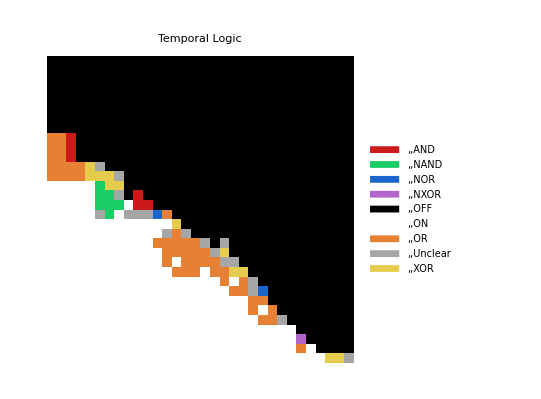

```mathematica
LabeledLogic=Table[
isTrue=Table[If[Count[hasSpiked[[kk,jj]],i]>3,1,0],{i,0,3}];
out=Logic[[Position[Logic,isTrue,Infinity][[1,1]],2]];
out,
{kk,1,size},{jj,1,size}];
MatLogic=Table[
isTrue=Table[If[Count[hasSpiked[[kk,jj]],i]>0,1,0],{i,0,3}];
out=Position[Logic,isTrue,Infinity][[1,1]],
{kk,1,size},{jj,1,size}];
grey=.65
red = RGBColor[.8,.1,.1]
orange=  RGBColor[.9,.5,.2]
yellow=RGBColor[.9,.8,.3]
green= RGBColor[.1,.8,.4]
blue =RGBColor[.1,.4,.8]
purple=RGBColor[.7,.4,.8]
ArrayPlot[LabeledLogic,ColorRules->
{"OFF"->Black,"ON"->White,"AND"->red,"OR"->orange,"XOR"->yellow,"NAND"->green,"NOR"->blue,"NXOR"->purple,"Unclear"->GrayLevel[grey],"NIMP1"->GrayLevel[grey],"NIMP2"->GrayLevel[grey],"AIMP1"->GrayLevel[grey],"AIMP2"->GrayLevel[grey],"XIMP1"->GrayLevel[grey],"XIMP2"->GrayLevel[grey],"IMP1"->GrayLevel[grey],"IMP2"->GrayLevel[grey]},PlotLegends->Automatic,DataRange->{{1.5,4.5},{-2.5,0.5}},FrameTicks->Automatic,FrameLabel->{"Inhibitory Bias","Excitatory Bias"},PlotLabel->Style["Temporal Logic","Title",Black,24]]
(*thresholded to ignore transient spikes*)
```

```mathematica
Table[{i,j},{i,-0.1,6.1,.4},{j,-2.2,4.,.4}]
```

{{{-0.1,-2.2},{-0.1,-1.8},{-0.1,-1.4},{-0.1,-1.},{-0.1,-0.6},{-0.1,-0.2},{-0.1,0.2},{-0.1,0.6},{-0.1,1.},{-0.1,1.4},{-0.1,1.8},{-0.1,2.2},{-0.1,2.6},{-0.1,3.},{-0.1,3.4},{-0.1,3.8}},{{0.3,-2.2},{0.3,-1.8},{0.3,-1.4},{0.3,-1.},{0.3,-0.6},{0.3,-0.2},{0.3,0.2},{0.3,0.6},{0.3,1.},{0.3,1.4},{0.3,1.8},{0.3,2.2},{0.3,2.6},{0.3,3.},{0.3,3.4},{0.3,3.8}},{{0.7,-2.2},{0.7,-1.8},{0.7,-1.4},{0.7,-1.},{0.7,-0.6},{0.7,-0.2},{0.7,0.2},{0.7,0.6},{0.7,1.},{0.7,1.4},{0.7,1.8},{0.7,2.2},{0.7,2.6},{0.7,3.},{0.7,3.4},{0.7,3.8}},{{1.1,-2.2},{1.1,-1.8},{1.1,-1.4},{1.1,-1.},{1.1,-0.6},{1.1,-0.2},{1.1,0.2},{1.1,0.6},{1.1,1.},{1.1,1.4},{1.1,1.8},{1.1,2.2},{1.1,2.6},{1.1,3.},{1.1,3.4},{1.1,3.8}},{{1.5,-2.2},{1.5,-1.8},{1.5,-1.4},{1.5,-1.},{1.5,-0.6},{1.5,-0.2},{1.5,0.2},{1.5,0.6},{1.5,1.},{1.5,1.4},{1.5,1.8},{1.5,2.2},{1.5,2.6},{1.5,3.},{1.5,3.4},{1.5,3.8}},{{1.9,-2.2},{1.9,-1.8},{1.9,-1.4},{1.9,-1.},{1.9,-0.6},{1.9,-0.2},{1.9,0.2},{1.9,0.6},{1.9,1.},{1.9,1.4},{1.9,1.8},{1.9,2.2},{1.9,2.6},{1.9,3.},{1.9,3.4},{1.9,3.8}},{{2.3,-2.2},{2.3,-1.8},{2.3,-1.4},{2.3,-1.},{2.3,-0.6},{2.3,-0.2},{2.3,0.2},{2.3,0.6},{2.3,1.},{2.3,1.4},{2.3,1.8},{2.3,2.2},{2.3,2.6},{2.3,3.},{2.3,3.4},{2.3,3.8}},{{2.7,-2.2},{2.7,-1.8},{2.7,-1.4},{2.7,-1.},{2.7,-0.6},{2.7,-0.2},{2.7,0.2},{2.7,0.6},{2.7,1.},{2.7,1.4},{2.7,1.8},{2.7,2.2},{2.7,2.6},{2.7,3.},{2.7,3.4},{2.7,3.8}},{{3.1,-2.2},{3.1,-1.8},{3.1,-1.4},{3.1,-1.},{3.1,-0.6},{3.1,-0.2},{3.1,0.2},{3.1,0.6},{3.1,1.},{3.1,1.4},{3.1,1.8},{3.1,2.2},{3.1,2.6},{3.1,3.},{3.1,3.4},{3.1,3.8}},{{3.5,-2.2},{3.5,-1.8},{3.5,-1.4},{3.5,-1.},{3.5,-0.6},{3.5,-0.2},{3.5,0.2},{3.5,0.6},{3.5,1.},{3.5,1.4},{3.5,1.8},{3.5,2.2},{3.5,2.6},{3.5,3.},{3.5,3.4},{3.5,3.8}},{{3.9,-2.2},{3.9,-1.8},{3.9,-1.4},{3.9,-1.},{3.9,-0.6},{3.9,-0.2},{3.9,0.2},{3.9,0.6},{3.9,1.},{3.9,1.4},{3.9,1.8},{3.9,2.2},{3.9,2.6},{3.9,3.},{3.9,3.4},{3.9,3.8}},{{4.3,-2.2},{4.3,-1.8},{4.3,-1.4},{4.3,-1.},{4.3,-0.6},{4.3,-0.2},{4.3,0.2},{4.3,0.6},{4.3,1.},{4.3,1.4},{4.3,1.8},{4.3,2.2},{4.3,2.6},{4.3,3.},{4.3,3.4},{4.3,3.8}},{{4.7,-2.2},{4.7,-1.8},{4.7,-1.4},{4.7,-1.},{4.7,-0.6},{4.7,-0.2},{4.7,0.2},{4.7,0.6},{4.7,1.},{4.7,1.4},{4.7,1.8},{4.7,2.2},{4.7,2.6},{4.7,3.},{4.7,3.4},{4.7,3.8}},{{5.1,-2.2},{5.1,-1.8},{5.1,-1.4},{5.1,-1.},{5.1,-0.6},{5.1,-0.2},{5.1,0.2},{5.1,0.6},{5.1,1.},{5.1,1.4},{5.1,1.8},{5.1,2.2},{5.1,2.6},{5.1,3.},{5.1,3.4},{5.1,3.8}},{{5.5,-2.2},{5.5,-1.8},{5.5,-1.4},{5.5,-1.},{5.5,-0.6},{5.5,-0.2},{5.5,0.2},{5.5,0.6},{5.5,1.},{5.5,1.4},{5.5,1.8},{5.5,2.2},{5.5,2.6},{5.5,3.},{5.5,3.4},{5.5,3.8}},{{5.9,-2.2},{5.9,-1.8},{5.9,-1.4},{5.9,-1.},{5.9,-0.6},{5.9,-0.2},{5.9,0.2},{5.9,0.6},{5.9,1.},{5.9,1.4},{5.9,1.8},{5.9,2.2},{5.9,2.6},{5.9,3.},{5.9,3.4},{5.9,3.8}}}